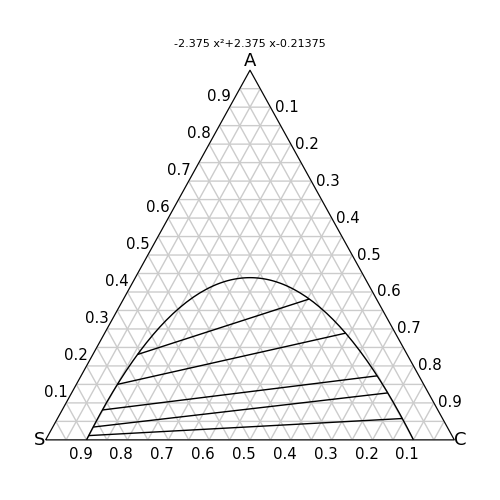

```mathematica
Module[{x1,y1,x2,y2,x3,y3,f,s,A1,B1,C1,g,xi,xf,xsol,tie1},
x1=0.1;y1=0;
x2=0.5;y2=0.38;
x3=0.9;y3=0;

f[x_]=a*x^2+b*x+c;

s=Solve[f[x1]==y1&&f[x2]==y2&&f[x3]==y3,{a,b,c}][[1]];
A1=a/.s;B1=b/.s;C1=c/.s;

g[x_]=A1*x^2+B1*x+C1;

xsol[y0_]=x/.Quiet@Solve[g[x]==y0,x];

Show[
Graphics[{
{GrayLevel[0.8],Thin,Table[{
Line[{{i/2,i*√3/2},{1-i/2,i*√3/2}}],
Line[{{i,0},{i/2,i*√3/2}}],
Line[{{1-i,0},{1-i/2,i*√3/2}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
Table[{Text[Style[1-j,15],{1.04-j/2,j*√3/2}],Rotate[Text[Style[j,15],{j/2-0.025,j*√3/2+0.025}],-55 Degree],Rotate[Text[Style[1-j,15],{j-0.015,-0.035}],55 Degree]},{j,0.1,0.9,0.1}],
Text[Style["A",18],{0.5,√3/2},{0,-1}],Text[Style["S  ",18],{0,0},{1,0}],Text[Style["  C",18],{1,0},{-1,0}],
(*tie1*)
{Thick,
Line[{{xsol[0.01][[1]],0.01},{xsol[0.05][[2]],0.05}}],
Line[{{xsol[0.03][[1]],0.03},{xsol[0.11][[2]],0.11}}],
Line[{{xsol[0.07][[1]],0.07},{xsol[0.15][[2]],0.15}}],
Line[{{xsol[0.13][[1]],0.13},{xsol[0.25][[2]],0.25}}],
Line[{{xsol[0.2][[1]],0.2},{xsol[0.33][[2]],0.33}}],
}
},AspectRatio->1],
Plot[g[x],{x,x1,x3},PlotStyle->{Thick,Black}],
ImageSize->{500,450},PlotLabel->g[x]]
]
```

```mathematica
Manipulate[
Show[
Graphics[{
{Thin,GrayLevel[0.8],
Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{0,1.025}],Text[Style["A",18],{1.025,0}],Text[Style["C",18],{-0.025,-0.025}],
BezierCurve[pts,SplineDegree->d],
(*{Thick,Line[pts]}*)
},AspectRatio->1],
ImageSize->{500,450}],
{{pts,{{0,0},{0.25,0.3},{0.5,0.5},{0.9,0}}},Locator,LocatorAutoCreate->True},{{d,3,"degree"},2,6,1}]
```

```mathematica
{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}
```

```mathematica
{{0.05,0},{0.05,0.6},{0.37,0.4},{0.97,0}}
```

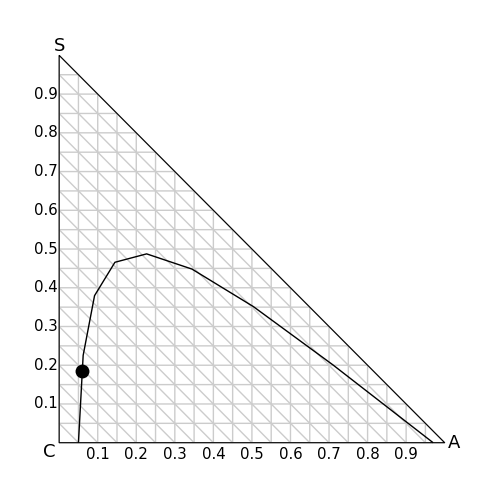

```mathematica
Module[{phase2},
phase2=BezierFunction[{{0.05,0},{0.065,0.7},{0.2,0.6},{0.97,0}},SplineDegree->3];
Show[
Graphics[{
{Thin,GrayLevel[0.8],
Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{0,1.025}],Text[Style["A",18],{1.025,0}],Text[Style["C",18],{-0.025,-0.025}],
BezierCurve[{{0.05,0},{0.065,0.7},{0.2,0.6},{0.97,0}},SplineDegree->3],
{PointSize[0.02],Point[phase2[0.1]]}
},AspectRatio->1],

ImageSize->{500,450}]]
```

```mathematica
√((0.5-0)^2+(√3/2-0)^2)
```

1.

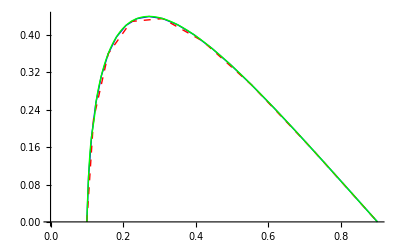

```mathematica
Module[{f,g,j},
f=BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}];
g=Interpolation[Table[f[i],{i,0,1,0.05}]];
j=Interpolation[Table[BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}][i],{i,0,1,0.05}]];

Show[
ListPlot[Table[f[i],{i,0,1,0.05}],Joined->True,PlotStyle->{Thick,Blue}],
Graphics[{Thick,Dashed,Red,BezierCurve[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}]}],
Plot[j[x],{x,0.1,0.9},PlotStyle->{Thick,Green}]
]
]
```

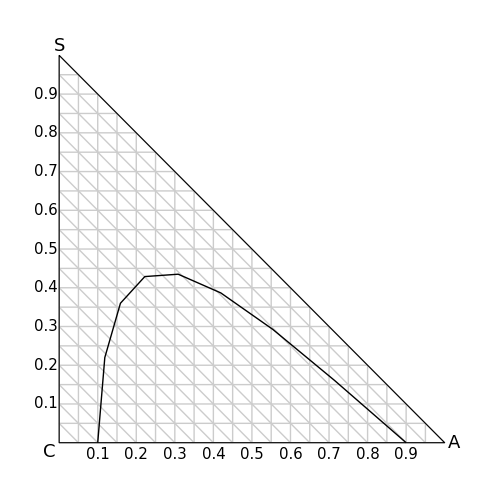

```mathematica
Module[{y},
y=Interpolation[Table[BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}][i],{i,0,1,0.025}]];

Show[
Graphics[{
{Thin,GrayLevel[0.8],
Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{0,1.025}],Text[Style["A",18],{1.025,0}],Text[Style["C",18],{-0.025,-0.025}],
{Thick,BezierCurve[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}]},
},AspectRatio->1],
ImageSize->{500,450}]
]
```